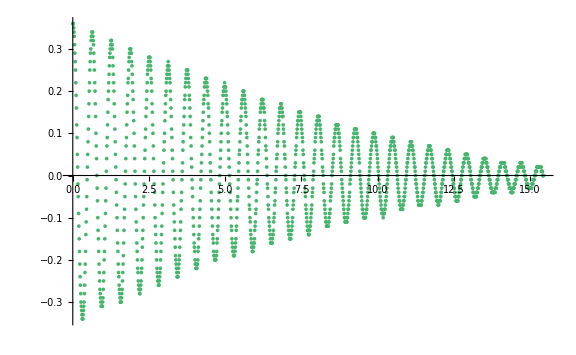

```mathematica
dir=NotebookDirectory[];
SetDirectory[dir];
file ="othernew.csv";
data = Drop[Import[file,"Table","FieldSeparators"->";"],81];
data = Drop[data,-1];
sdata =  MapAt[(#-data[[1,1]])&,data,{All,1}];
ListPlot[sdata,ImageSize->Large]
Δt = sdata[[2,1]]-sdata[[1,1]];
timestart = sdata[[1,1]];
timestop = sdata[[Length[sdata],1]];
(*dir=NotebookDirectory[];
SetDirectory[dir];
file ="othernew.csv";
(*starttheta = Last[Import[file,"Table","FieldSeparators"->";"]][[2]];*)
data = Drop[Import[file,"Table","FieldSeparators"->";"],-1];
d1 = Drop[data,80];
sf1 = MapAt[(#-d1[[1,1]])&,d1,{All,1}];
sdata = MapAt[(#-0.002940824254723355)&,sf1,{All,2}];
Δt = sdata[[2,1]];
timestart = sdata[[1,1]];
timestop = sdata[[Length[sdata],1]];
Δϕ = (sdata[[1,2]] - sdata[[Length[sdata],2]]);
listplot =ListPlot[sdata,ImageSize->Large,PlotRange->All]
1/2(Mean[Select[sdata[[All,2]],#> 0&]]-Abs@Mean[Select[sdata[[All,2]],#< 0&]])*)
```

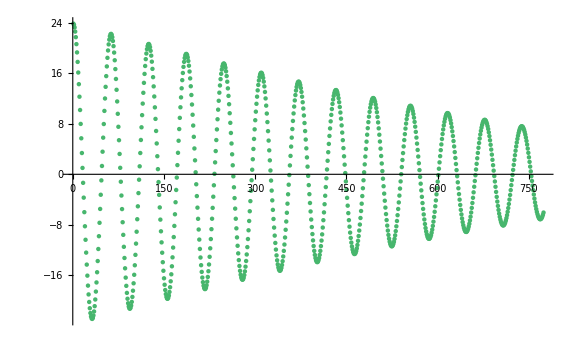

```mathematica
corrdata = Table[data[[i,2]], {i,1,Length[data]}];
corr=ListCorrelate[Take[corrdata,Quotient[Length[corrdata],2]],corrdata];
ListPlot[corr,ImageSize->Large]
```

```mathematica
gaps=Length/@Rest@Most@Split[UnitStep@Differences[corr],#1≤#2&];
per = Mean[N[gaps]] Δt;
params = {mb->0.0983,mw->0.177,l->0.0798,g->9.81, k -> 0.09};
inertia=𝒿 /. First[Solve[{((mb l+mw k) g)/𝒿==(2π 1/per)^2},𝒿] /. params];
Solve[√((g( mb l + mw k ))/𝒿) == 2 π/per,𝒿] /. params
```

{{𝒿→0.00222454}}

```mathematica
f=2/(√(Length@sdata[[All,2]]))Abs@Fourier[sdata[[All,2]]];
peaksize= Last[TakeLargest[f,2]];
peaks= Flatten[Position[f,x_ /; x≥ peaksize]];
pos = First[peaks];
n = Length@sdata[[All,2]];
```

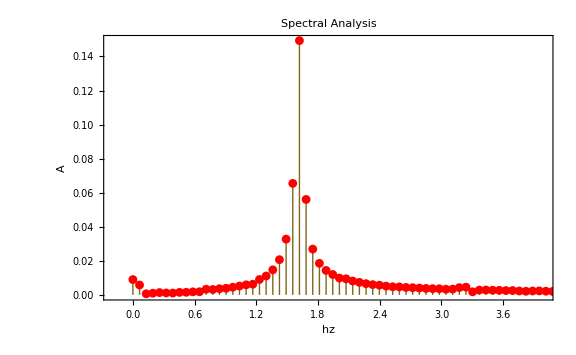

```mathematica
ListPlot[f,Filling->Axis,DataRange->{0,(n-1)/Last@sdata[[All,1]]}, PlotRange->{{-0.2,4},All},PlotStyle->{{Red,PointSize[0.011]}},ImageSize->Large, PlotLabel->"Spectral Analysis",FrameLabel->{"hz","A"},Frame -> True, FrameStyle->Black]
```

```mathematica
fr = Abs[Fourier[sdata Exp[2 Pi I (pos - 2) N[Range[0, n - 1]]/n], FourierParameters->{0,2/n}]];
frpos = Position[fr, Max[fr]][[1,1]];
period=N[n/(pos - 2 + 2 (frpos - 1)/n)] Δt
Solve[√(g/l)== 2 π/T,l] /. {T -> period, g -> 9.81}
```

0.609028

{{l→0.0921688}}

```mathematica
physpendulum =ParametricNDSolveValue[{Θ x''[t]+ (mb l+mw k) g  Sin[x[t]]==-μ(Tanh[x'[t]/0.1])- rb x'[t]/. params,x[0]==sdata[[1,2]],x'[0]==0 },x,{t,timestop+1},{μ,Θ,rb}];
```

```mathematica
Manipulate[Plot[#[t]& @ physpendulum[μ,Θ,rb] ,{t,0,timestop+1},Epilog->{Red,Point[sdata]},ImageSize->{GoldenRatio 300,300},PlotPoints-> 50,PlotRange->{{0,timestop+1},{-0.4,0.4}},PlotPoints->200, Frame->True, FrameStyle->Black],{μ,1 10^-5,1 10^-4,Appearance -> "Labeled"},{{Θ,inertia},inertia-inertia/2,inertia+inertia/2,Appearance -> "Labeled"},{rb,1 10^-5,1 10^-3,Appearance -> "Labeled"}]
```

```mathematica
nmodel[𝒿_?NumberQ,μ_?NumberQ,rb_?NumberQ] :=  (nmodel[𝒿,μ,rb]=Module[{x,t},First[x/.NDSolve[{𝒿 x''[t]+ (mb l+mw k) g  Sin[x[t]]==-μ(Tanh[x'[t]/0.1])- rb x'[t]/. {mb->0.0983,mw->0.177,g->9.81, k -> 0.09, l -> 0.0798},x[0]==sdata[[1,2]],x'[0]==0 },x,{t,0,Last@sdata[[All,1]]}]]])
```

```mathematica
nfit=NonlinearModelFit[sdata,nmodel[𝒿,μ,rb][t],{{𝒿,0.002224538442941061},{μ,0.00007345},{rb,0.00048619}},t,Method->"ConjugateGradient"]
nfit["BestFitParameters"]
```

FittedModel[InterpolatingFunction[…][t]]

{𝒿→0.00225167,μ→0.000201746,rb→0.000482963}

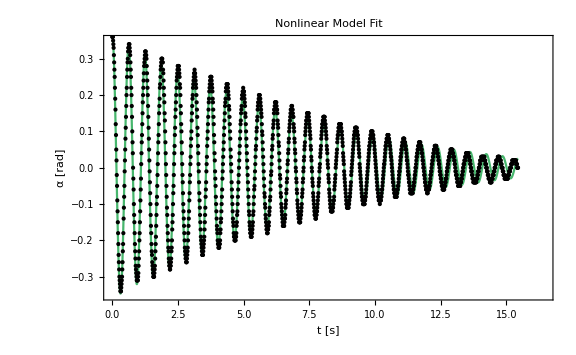

```mathematica
Plot[{nfit[t]},{t,0,Last@sdata[[All,1]]},Epilog-> {Black,Point[sdata]},PlotPoints-> 50,PlotRange->{{0,timestop+1},{-0.35,0.35}},PlotPoints->200, Frame->True, FrameStyle->Black,PlotLabel->"Nonlinear Model Fit", FrameLabel->{"t [s]","α [rad]"},ImageSize->Large]
```